```mathematica
a[n_]:=a[n]=Sqrt[2-2 Sqrt[1-(a[n-1]/2)^2]]
a[0]=1;
s[n_]:=3 2^(n-1)*a[n-1];
t=Table[{n,6*2^n,N[s[n],48],N[2 s[n+1]-s[n],48]},{n,1,48}];
t1=Prepend[t,{"分割数","边数","下界","上界"}];
GridBox[t1,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

分割数 | 边数 | 下界 | 上界
1 | 12 | 3. | 3.21165708246049829637357210297715988037765363168
2 | 24 | 3.10582854123024914818678605148857994018882681584 | 3.15942868533222724613671288749489254911072701512
3 | 48 | 3.13262861328123819716174946949173624464977691548 | 3.14607179281249621710854417292510613365092426324
4 | 96 | 3.13935020304686720713514682120842118915035058936 | 3.14271369873415206908755903171089902492247384296
5 | 192 | 3.14103195089050963811135292645966010703641221616 | 3.14187299368041451278986569146279118345891239294
6 | 384 | 3.14145247228546207545060930896122564524766230455 | 3.14166274353825321558231738129849343776109065463
7 | 768 | 3.14155760791185764551646334512985954150437647959 | 3.14161017638477917182147586231244715953571335197
8 | 1536 | 3.14158389214831840866896960372115335052004491578 | 3.14159703430778178280794740814075009658851970157
9 | 3072 | 3.14159046322805009573845850593095172355428230868 | 3.14159374877049300535109477528928298270071220126
10 | 6144 | 3.14159210599927155054477664061011735312749725497 | 3.14159292738504334464097152892754645880794052977
11 | 12288 | 3.14159251669215744759287408476883190596771889237 | 3.14159272203861046278622453936180617847666655882
12 | 24576 | 3.14159261936538395518954931206531904222219272559 | 3.14159267070199783815473370577315778322305329689
13 | 49152 | 3.14159264503369089667214150891923841272262301124 | 3.14159265786784440673636577206519962817423193353
14 | 98304 | 3.14159265145076765170425364049221902044842747239 | 3.14159265465930603167799272033872938406612613939
15 | 196608 | 3.14159265305503684169112318041547420225727680589 | 3.14159265385717143683816313881468246045140616897
16 | 393216 | 3.14159265345610413926464315961507833135434148743 | 3.14159265365663778806100347349314839719548552094
17 | 786432 | 3.14159265355637096366282331655411336427491350418 | 3.14159265360650437586251341529103699346578551056
18 | 1572864 | 3.14159265358143766976266836592257517887034950737 | 3.14159265359397102281262839187351919263013222712
19 | 3145728 | 3.14159265358770434628764837889804718575024086725 | 3.14159265359083768455014072921495276185057189042
20 | 6291456 | 3.14159265358927101541889455405649997380040637883 | 3.14159265359005434998451778812504946617155237949
21 | 12582912 | 3.14159265358966268270170617109077471998597937916 | 3.14159265358985851634311198876349478672625091277
22 | 25165824 | 3.14159265358976059952240907992713475335611514596 | 3.14159265358980955793276053491753868839416422021
23 | 50331648 | 3.14159265358978507872758480742233672087513968309 | 3.14159265358979731833017267120570169953171348508
24 | 100663296 | 3.14159265358979119852887873931401921020342658409 | 3.14159265358979425842952570526209570454863638369
25 | 201326592 | 3.14159265358979272847920222228805745737603148389 | 3.14159265358979349345436396377521628406740058066
26 | 402653184 | 3.14159265358979311096678309303163687072171603227 | 3.1415926535897933022105735284034353088386249719
27 | 805306368 | 3.14159265358979320658867831071753608978017050209 | 3.14159265358979325439962591956048624502465190358
28 | 1610612736 | 3.14159265358979323049415211513901116740241120283 | 3.14159265358979324244688901734974874032073493862
29 | 3221225472 | 3.14159265358979323647052056624437995386157307073 | 3.14159265358979323945870479179706434922285421626
30 | 6442450944 | 3.14159265358979323796461267902072215154221364349 | 3.1415926535897932387116587354088932505157651931
31 | 12884901888 | 3.1415926535897932383381357072148077010289894183 | 3.14159265358979323852489722131185047578070425965
32 | 25769803776 | 3.14159265358979323843151646426332908840484683897 | 3.14159265358979323847820684278758978209329598393
33 | 51539607552 | 3.14159265358979323845486165352545943524907141145 | 3.14159265358979323846653424815652460867121622486
34 | 103079215104 | 3.14159265358979323846069795084099202196014381816 | 3.14159265358979323846361609949875831531568205445
35 | 206158430208 | 3.14159265358979323846215702516987516863791293631 | 3.14159265358979323846288656233431674197679762244
36 | 412316860416 | 3.14159265358979323846252179375209595530735527937 | 3.14159265358979323846270417804320634864207645885
37 | 824633720832 | 3.14159265358979323846261298589765115197471586911 | 3.14159265358979323846265858197042875030839616447
38 | 1649267441664 | 3.14159265358979323846263578393403995114155601679 | 3.14159265358979323846264718295223435072497609066
39 | 3298534883328 | 3.14159265358979323846264148344313715093326605373 | 3.1415926535897932384626443331976857508291210722
40 | 6597069766656 | 3.14159265358979323846264290832041145088119356296 | 3.14159265358979323846264362075904860085515731758
41 | 13194139533312 | 3.14159265358979323846264326453973002586817544027 | 3.14159265358979323846264344264938931336166637893
42 | 26388279066624 | 3.1415926535897932384626433535945596696149209096 | 3.14159265358979323846264339812197449148829364426
43 | 52776558133248 | 3.14159265358979323846264337585826708055160727693 | 3.1415926535897932384626433869901207860199504606
44 | 105553116266496 | 3.14159265358979323846264338142419393328577886876 | 3.14159265358979323846264338420715735965286466468
45 | 211106232532992 | 3.14159265358979323846264338281567564646932176672 | 3.1415926535897932384626433835114165030610932157
46 | 422212465065984 | 3.14159265358979323846264338316354607476520749121 | 3.14159265358979323846264338333748128891315035346
47 | 844424930131968 | 3.14159265358979323846264338325051368183917892233 | 3.1415926535897932384626433832939974853761646379
48 | 1688849860263936 | 3.14159265358979323846264338327225558360767178011 | 3.14159265358979323846264338328312653449191820901

```mathematica
tt=Table[{n,6*2^n,N[4/3 s[n+1]-1/3 s[n],18]},{n,1,12}];
tt1=Prepend[tt,{"分割数","边数","近似值"}];
GridBox[tt1,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
N[Pi,18]
```

分割数 | 边数 | 近似值
1 | 12 | 3.1411047216403322
2 | 24 | 3.14156197063156788
3 | 48 | 3.14159073296874354
4 | 96 | 3.14159253350505712
5 | 192 | 3.14159264608377955
6 | 384 | 3.14159265312065617
7 | 768 | 3.141592653560472
8 | 1536 | 3.14159265358796066
9 | 3072 | 3.1415926535896787
10 | 6144 | 3.14159265358978608
11 | 12288 | 3.14159265358979279
12 | 24576 | 3.14159265358979321

3.14159265358979324

```mathematica
y[0]=1/Sqrt[2];x[0]=1/2;
y[n_]:=y[n]=(1-Sqrt[1-y[n-1]^2])/(1+Sqrt[1-y[n-1]^2]);
x[n_]:=x[n]=(1+y[n])^2*x[n-1]-2^n*y[n];
Table[N[1/x[n],45],{n,1,5}]
N[Pi,45]
```

{2.91421356237309504880168872420969807856967188,3.14057925052216824831133126897582331177344024,3.14159264621354228214934443198269577431443722,3.1415926535897932382795127748018639743812255,3.14159265358979323846264338327950288419711468}

3.1415926535897932384626433832795028841971694

```mathematica
Clear[x,y,h,k,a,b,n,m,r1,g,r,ls,lss,s,x1,lp,l,sol1];
sol=Solve[{y-b==k*(x-a),(x-a)^2+(y-b)^2==h^2},{x,y}]//Simplify;
```

```mathematica
sol1=Flatten[sol];
```

{{x→(a+a k^2-√(h^2 (1+k^2)))/(1+k^2),y→(b+b k^2-k √(h^2 (1+k^2)))/(1+k^2)},{x→(a+a k^2+√(h^2 (1+k^2)))/(1+k^2),y→(b+b k^2+k √(h^2 (1+k^2)))/(1+k^2)}}

m=1000

r=318

P=3.14465

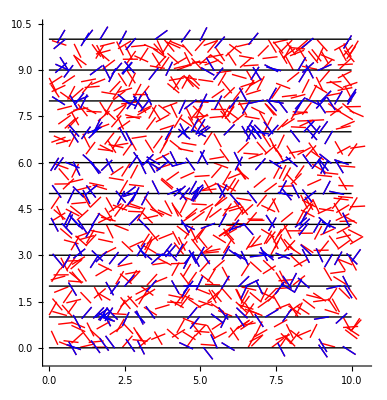

```mathematica
x[a_,b_,h_,k_]:=(a+a k^2+√(h^2 (1+k^2)))/(1+k^2);
y[a_,b_,h_,k_]:=(b+b k^2+k √(h^2 (1+k^2)))/(1+k^2);
h=1/2;
m=1000;
a=Table[Random[Real,{0,10},6],{n,m}];
b=Table[Random[Real,{0,10},6],{n,m}];
k=Table[Random[Real,{-2.1,2.1},10],{n,m}];
g=Table[Graphics[{RGBColor[1,0,0],Line[{{a[[n]],b[[n]]},{x[a[[n]],b[[n]],h,k[[n]]],y[a[[n]],b[[n]],h,k[[n]]]}}]}],{n,m}];
r1=Table[Graphics[Line[{{0,k},{10,k}}]],{k,0,10}];
x1[a_,b_,k_,l_]:=-((b-a*k-2*h*l)/k);
r=0;
ls={};
For[n=1,n<m+1,n++,For[l=0,l<11,l++,If[a[[n]]≤x1[a[[n]],b[[n]],k[[n]],l]≤x[a[[n]],b[[n]],h,k[[n]]],r=r+1;ls=Append[ls,{{a[[n]],b[[n]]},{x[a[[n]],b[[n]],h,k[[n]]],y[a[[n]],b[[n]],h,k[[n]]]}}]]]];
lss=Flatten[ls];
s=Length[lss];
lp=Table[Graphics[{RGBColor[0,0,1],Line[{{lss[[4*k+1]],lss[[4*k+2]]},{lss[[4*k+3]],lss[[4*k+4]]}}]}],{k,0,s/4-1}];
Print["m=",m]
Print["r=",r]
Print["P=",m/r//N]
Show[g,r1,lp,Axes->True,AspectRatio->Automatic]
```

3.1496

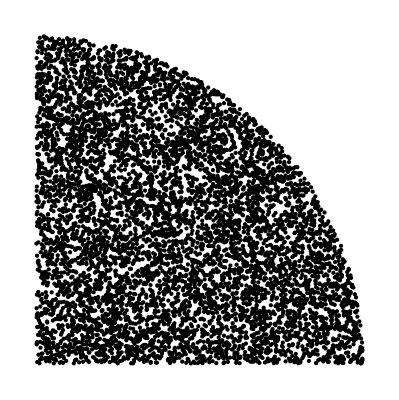

```mathematica
Clear[a,n,a1,i];
a={};
n=10000;
Table[a1={Random[Real,{0,1}],Random[Real,{0,1}]};If[a1[[1]]^2+a1[[2]]^2≤1,a=Append[a,a1]],{i,1,n}];
4 Length[a]/n//N
Show[Graphics[Point[a]]]
```

```mathematica
Clear[P];
```

```mathematica
P1=3.1;
```

```mathematica
P2=P1+Sin[P1]
```

3.14158

```mathematica
P3=10^20*(Pi-(P2+Sin[P2]))
```

0.

```mathematica
P=3.10;
```

```mathematica
table={{1,P}};
```

```mathematica
Clear[n,i,P,table]
```

```mathematica
n=20;
For[i=1,i≤n,i++,P=P+Sin[P];table=Append[table,{i+1,P}]];
```

```mathematica
table
```

{{1,3.1},{2,3.14159},{3,3.14159},{4,3.14159},{5,3.14159},{6,3.14159},{7,3.14159},{8,3.14159},{9,3.14159},{10,3.14159},{11,3.14159},{12,3.14159},{13,3.14159},{14,3.14159},{15,3.14159},{16,3.14159},{17,3.14159},{18,3.14159},{19,3.14159},{20,3.14159},{21,3.14159}}

```mathematica
table1={};
```

```mathematica
For[i=1,i≤n,i++,table1=Append[table1,Rationalize[table[[i,2]],10^(-9)]]]
```

```mathematica
table1
```

{31/10,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,312689/99532,31/10,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102,103993/33102}

```mathematica
Clear[table1,i,j,x2];
```

```mathematica
table
```

{{1,3.1},{2,3.14159},{3,3.14159},{4,3.14159},{5,3.14159},{6,3.14159},{7,3.14159},{8,3.14159},{9,3.14159},{10,3.14159},{11,3.14159},{12,3.14159},{13,3.14159},{14,3.14159},{15,3.14159},{16,3.14159},{17,3.14159},{18,3.14159},{19,3.14159},{20,3.14159},{21,3.14159}}

```mathematica
x2=3.1;
```

```mathematica
table1={};
For[i=1,i≤n,i++,x2=x2+Sin[x2];j=0;While[Abs[IntegerPart[10^(j) Pi]-IntegerPart[10^(j) x2]]==0,j++];table1=Append[table1,j-1];j=0]
```

```mathematica
table1
```

{4,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

```mathematica
x2=3.1;
```

```mathematica
x5=x4+Sin[x4]
```

3.14159

```mathematica
Rationalize[Pi,10^(-2)]
```

22/7

```mathematica
Rationalize[x3,10^(-7)]
```

4571/1455

```mathematica
IntegerPart[10^20Pi]
```

314159265358979323846

```mathematica
IntegerPart[10^20 x5]
```

314159265358979334144

```mathematica
y1=3.1;
y2=y1+Sin[y1];
y3=y2+Sin[y2];
y4=y3+Sin[y3]
y5=y4+Sin[y4]
```

3.14159

3.14159

```mathematica
10^30*Sin[y4]
10^30*Sin[y3]
```

1.22465×10^14

1.22465×10^14

```mathematica
IntegerPart[10^1000 y4]
IntegerPart[10^1000 y5]
```

31415926535897931159979634685441851614951405991398038513634543696357084398126974393677259966484293674319826570478572071370171049797107656965263309248627086464657823424094274249396433955622325987235244925380785211220595360019005499929713067419972361644155820640535629831962080844991375473485019953965702932073827693311949865419149466722467400721263270387570765834088227166689373320726497901424872361228457797834451905438366007947374429148578581242824622506298166778424062490776918620982051950831417332417310651464817366076361083268735570404720883005196517118283410890461812384239492036186487723173366846496296011914982227591417953294284520751985639223131671288689105988434420300277747062916241014249943086183976366698478587080502174301278271455331329867898632864176777361043599112949375846625082788785819699676983676274205812632942761923891434247690985184766094896996431074575246453227236350066936328843266536980676092769222851690691192129548588117997429812900166365181717916832963627470996112131751936

31415926535897931159979634685441851614951405991398038513634543696357084398126974393677259966484293674319826570478572071370171049797107656965263309248627086464657823424094274249396433955622325987235244925380785211220595360019005499929713067419972361644155820640535629831962080844991375473485019953965702932073827693311949865419149466722467400721263270387570765834088227166689373320726497901424872361228457797834451905438366007947374429148578581242824622506298166778424062490776918620982051950831417332417310651464817366076361083268735570404720883005196517118283410890461812384239492036186487723173366846496296011914982227591417953294284520751985639223131671288689105988434420300277747062916241014249943086183976366698478587080502174301278271455331329867898632864176777361043599112949375846625082788785819699676983676274205812632942761923891434247690985184766094896996431074575246453227236350066936328843266536980676092769222851690691192129548588117997429812900166365181717916832963627470996112131751936

```mathematica
(10^100 Pi-10^100 y5)
```

0.

```mathematica
Clear[y1,y2,y3,y4,y5];
```

```mathematica
y1=3.1;
y2=y1+Sin[y1];
y3=y2+Sin[y2];
y4=y3+Sin[y3];
y5=y4+Sin[y4];
```

```mathematica
IntegerPart[10^100*y3]
IntegerPart[10^100*y4]
IntegerPart[10^100*y5]
```

31415926535897931435667303171173228699167550981710022285650709387251316616699277811329625584350265344

31415926535897931435667303171173228699167550981710022285650709387251316616699277811329625584350265344

31415926535897931435667303171173228699167550981710022285650709387251316616699277811329625584350265344